Exercício 1

### y' = 3 - 2y

```mathematica
solucaoDif=DSolve[y'[x]==3-2y[x],y[x],x];
```

```mathematica
solveC1=Solve[y==solucaoDif[[1,1,2]],C[1]];
```

```mathematica
c1[x_,y_]:=solveC1[[1,1,2]];
```

```mathematica
campoDirecao[x_,y_]:={1,3-2y}
```

```mathematica
contornosC1=ContourPlot[c1[x,y],{x,-3,3},{y,-3,3},ContourShading->False,Contours->20,PlotPoints->50,ContourLabels->True];
```

```mathematica
streamDir=StreamPlot[campoDirecao[x,y],{x,-3,3},{y,-3,3}];
```

```mathematica
vectorDir=VectorPlot[campoDirecao[x,y],{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black}];
```

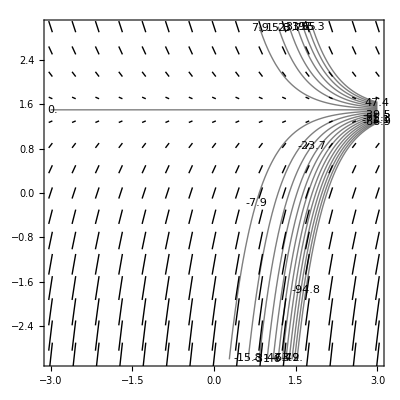

```mathematica
Show[contornosC1,vectorDir]
```

Exercício 2

### y’ = 2y - 3

```mathematica
solucaoDif1=DSolve[y'[x]==2y[x]-3,y[x],x]
```

{{y[x]→3/2+ⅇ^(2 x) C[1]}}

```mathematica
solveC1a=Solve[y==solucaoDif1[[1,1,2]],C[1]]
```

{{C[1]→1/2 ⅇ^(-2 x) (-3+2 y)}}

```mathematica
c1a[x_,y_]:=solveC1a[[1,1,2]]
```

```mathematica
campoDirecao1[x_,y_]:={1,2y-3}
```

```mathematica
contornosC1a=ContourPlot[c1a[x,y],{x,-3,3},{y,-3,3},ContourShading->False,Contours->20,PlotPoints->50,ContourLabels->True];
```

```mathematica
streamDir1=StreamPlot[campoDirecao1[x,y],{x,-3,3},{y,-3,3}];
```

```mathematica
vectorDir1=VectorPlot[campoDirecao1[x,y],{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black}];
```

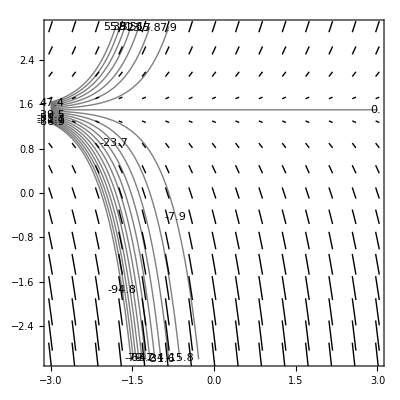

```mathematica
Show[contornosC1a,vectorDir1]
```

Exercício 3

### y’ = 3 + 2y

```mathematica
solveDif2=DSolve[y'[x]==3+2y[x],y[x],x];
```

```mathematica
solvec1b=Solve[y==solveDif2[[1,1,2]],C[1]];
```

```mathematica
c1b[x_,y_]:=solvec1b[[1,1,2]]
```

```mathematica
campoDirecao2[x_,y_]:={1,3+2y}
```

```mathematica
contornosC1b=ContourPlot[c1b[x,y],{x,-3,3},{y,-3,3},ContourShading->False,Contours->20,PlotPoints->50,ContourLabels->True];
```

```mathematica
streamDir2=StreamPlot[campoDirecao2[x,y],{x,-3,3},{y,-3,3}];
```

```mathematica
vectorDir2=VectorPlot[campoDirecao2[x,y],{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black}];
```

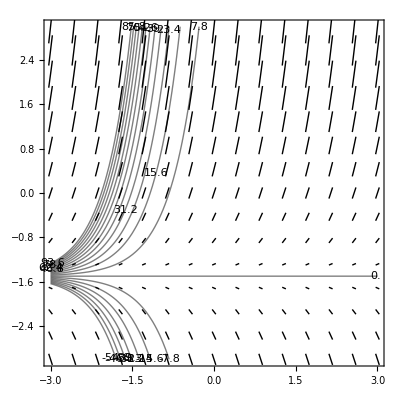

```mathematica
Show[contornosC1b,vectorDir2]
```

Exercício 4

### y’ = -1 - 2y

```mathematica
solveDif3=DSolve[y'[x]==-1-2y[x],y[x],x];
```

```mathematica
solvec1c=Solve[y==solveDif3[[1,1,2]],C[1]];
```

```mathematica
c1c[x_,y_]:=solvec1c[[1,1,2]]
```

```mathematica
campoDirecao3[x_,y_]:={1,-1-2y}
```

```mathematica
contornosC1c=ContourPlot[c1c[x,y],{x,-3,3},{y,-3,3},ContourShading->False,Contours->20,PlotPoints->50,ContourLabels->True];
```

```mathematica
streamDir3=StreamPlot[campoDirecao3[x,y],{x,-3,3},{y,-3,3}];
```

```mathematica
vectorDir3=VectorPlot[campoDirecao3[x,y],{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black}];
```

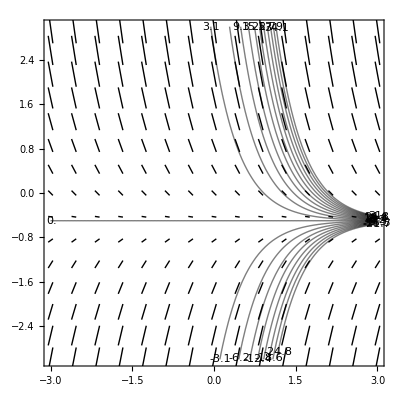

```mathematica
Show[contornosC1c,vectorDir3]
```

Exercício 5

### y’ = 1 + 2y

```mathematica
solveDif4=DSolve[y'[x]==1+2y[x],y[x],x];
```

```mathematica
solvec1d=Solve[y==solveDif4[[1,1,2]],C[1]];
```

```mathematica
c1d[x_,y_]:=solvec1d[[1,1,2]]
```

```mathematica
campoDirecao4[x_,y_]:={1,1+2y}
```

```mathematica
contornosC1d=ContourPlot[c1d[x,y],{x,-3,3},{y,-3,3},ContourShading->False,Contours->20,PlotPoints->50,ContourLabels->True];
```

```mathematica
streamDir4=StreamPlot[campoDirecao4[x,y],{x,-3,3},{y,-3,3}];
```

```mathematica
vectorDir4=VectorPlot[campoDirecao4[x,y],{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black}];
```

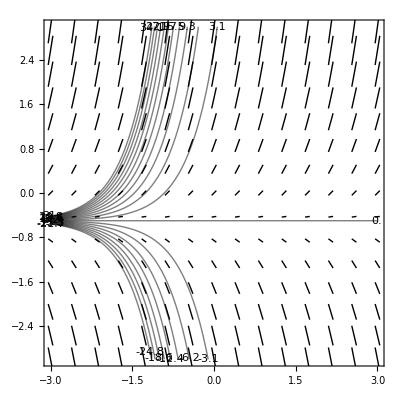

```mathematica
Show[contornosC1d,vectorDir4]
```

Exercício 6

### y’ = y + 2

```mathematica
solveDif5=DSolve[y'[x]==y[x]+2,y[x],x];
```

```mathematica
solvec1e=Solve[y==solveDif5[[1,1,2]],C[1]];
```

```mathematica
c1e[x_,y_]:=solvec1e[[1,1,2]]
```

```mathematica
campoDirecao5[x_,y_]:={1,y+2}
```

```mathematica
contornosC1e=ContourPlot[c1e[x,y],{x,-3,3},{y,-3,3},ContourShading->False,Contours->20,PlotPoints->50,ContourLabels->True];
```

```mathematica
streamDir5=StreamPlot[campoDirecao5[x,y],{x,-3,3},{y,-3,3}];
```

```mathematica
vectorDir5=VectorPlot[campoDirecao5[x,y],{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black}];
```

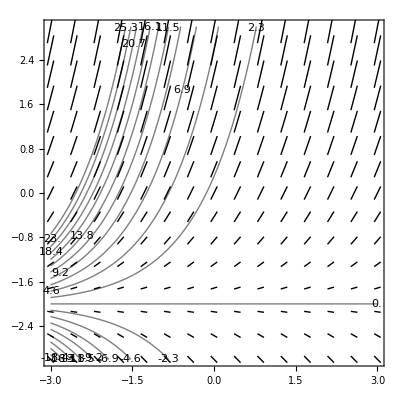

```mathematica
Show[contornosC1e,vectorDir5]
```

Exercícios do 7 ao 10

Exercício 7

Todas as soluções tendem a y = 3

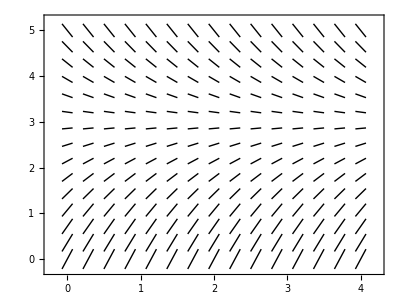

```mathematica
VectorPlot[{1,-y+3},{x,0,4},{y,0,5},VectorStyle->{Thick,Arrowheads[0],Black},AspectRatio->3/4]
```

Exercício 8

Todas as soluções tendem a y = 2/3

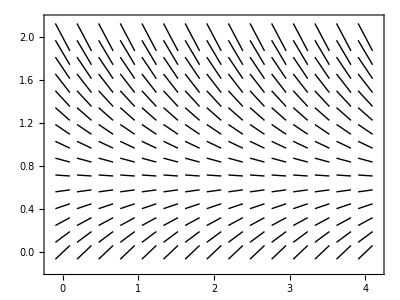

```mathematica
VectorPlot[{1,-y+2/3},{x,0,4},{y,0,2},VectorStyle->{Thick,Arrowheads[0],Black},AspectRatio->3/4]
```

Exercício 9

Todas as outras soluções se afastam de y = 2

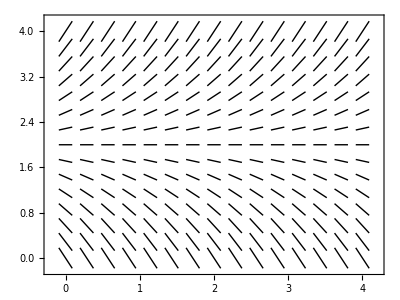

```mathematica
VectorPlot[{1,y-2},{x,0,4},{y,0,4},VectorStyle->{Thick,Arrowheads[0],Black},AspectRatio->3/4]
```

Exercício 10

Todas as outras soluções se afastam de y = 1/3

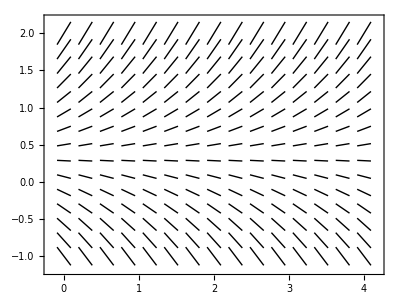

```mathematica
VectorPlot[{1,y-1/3},{x,0,4},{y,-1,2},VectorStyle->{Thick,Arrowheads[0],Black},AspectRatio->3/4]
```

Exercício 11

### y' = y (4 - y)

```mathematica
solveDif11=DSolve[y'[x]==y[x](4-y[x]),y[x],x];
```

```mathematica
field11[x_,y_]:={1,y(4-y)}
```

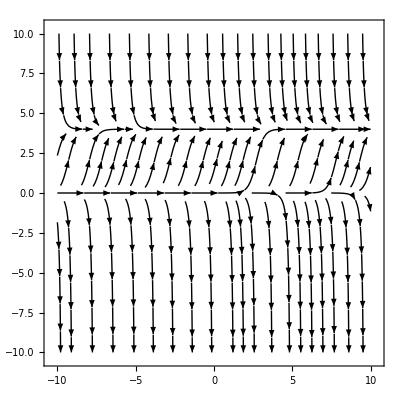

```mathematica
stream11=StreamPlot[field11[x,y],{x,-10,10},{y,-10,10},StreamStyle->{Black}]
```

Exercício 12

### y' = - y (5 - y)

```mathematica
solveDif12=DSolve[y'[x]==-y[x](5-y[x]),y[x],x]
```

{{y[x]→5/(1+ⅇ^(5 x+5 C[1]))}}

```mathematica
field12[x_,y_]:={1,-y(5-y)}
```

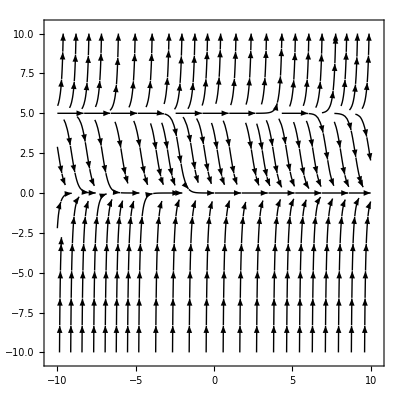

```mathematica
stream12=StreamPlot[field12[x,y],{x,-10,10},{y,-10,10},StreamStyle->{Black}]
```

Exercício 13

### y’ = y^2

```mathematica
solveDif13=DSolve[y'[x]==y[x]^2,y[x],x]
```

{{y[x]→1/(-x-C[1])}}

```mathematica
field13[x_,y_]:={1,y^2}
```

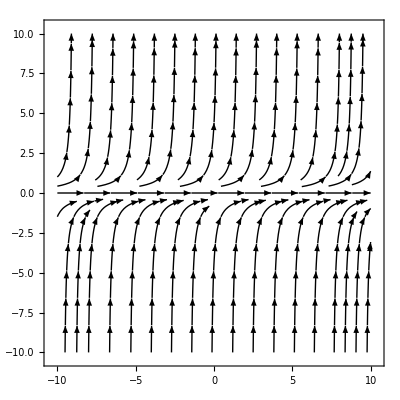

```mathematica
stream13=StreamPlot[field13[x,y],{x,-10,10},{y,-10,10},StreamStyle->{Black}]
```

Exercício 14

### y' =y (y - 2)^2

```mathematica
solveDif14=DSolve[y'[x]==y[x](y[x]-2)^2,y[x],x]
```

{{y[x]→InverseFunction[1/4 (-Log[-2+#1]+Log[#1]-2/(-2+#1))&][x+C[1]]}}

```mathematica
field14[x_,y_]:={1,y(y-2)^2}
```

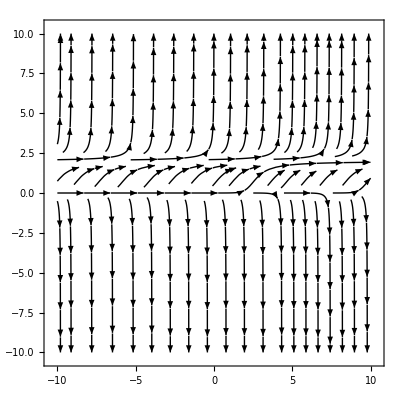

```mathematica
stream14=StreamPlot[field14[x,y],{x,-10,10},{y,-10,10},StreamStyle->{Black}]
```

### Campos de direção para os exercícios do 15 ao 20

(a)

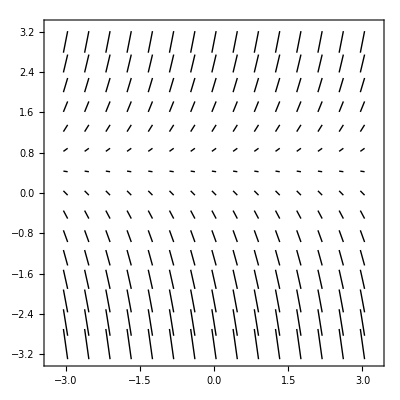

```mathematica
streamA=VectorPlot[{1,2y-1},{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black,Thick}]
```

(b) FIG 1.1.8

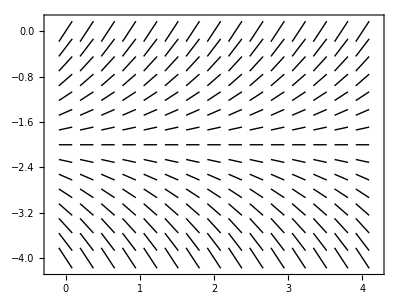

```mathematica
streamB=VectorPlot[{1,2+y},{x,0,4},{y,-4,0},VectorStyle->{Arrowheads[0],Black,Thick},AspectRatio->3/4]
```

(c) FIG 1.1.6

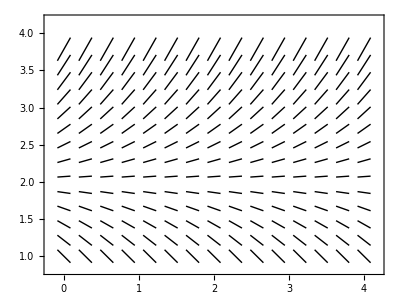

```mathematica
streamC=VectorPlot[{1,y-2},{x,0,4},{y,1,4},VectorStyle->{Arrowheads[0],Black,Thick},AspectRatio->3/4]
```

(d)

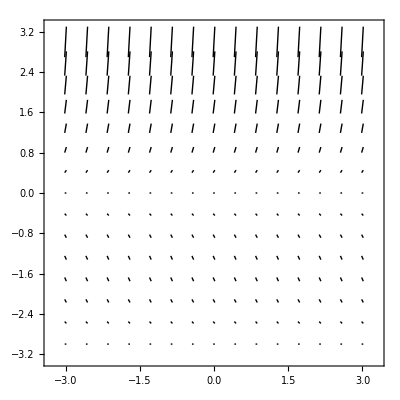

```mathematica
vectorD=VectorPlot[{1,y(y+3)},{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black,Thick}]
```

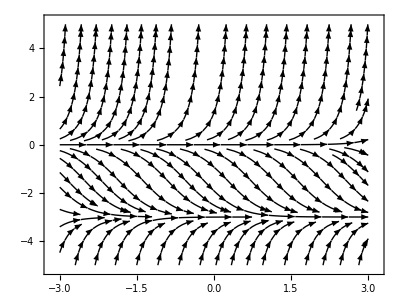

```mathematica
streamD=StreamPlot[{1,y(y+3)},{x,-3,3},{y,-5,5},AspectRatio->3/4,StreamStyle->{Black}]
```

(e) FIG 1.1.10

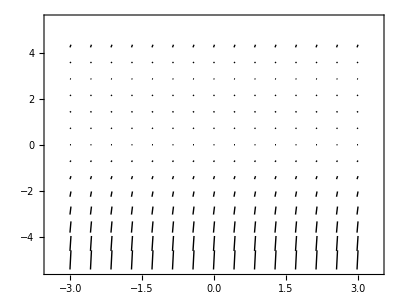

```mathematica
vectorE=VectorPlot[{1,y(y-3)},{x,-3,3},{y,-5,5},VectorStyle->{Arrowheads[0],Black,Thick},AspectRatio->3/4]
```

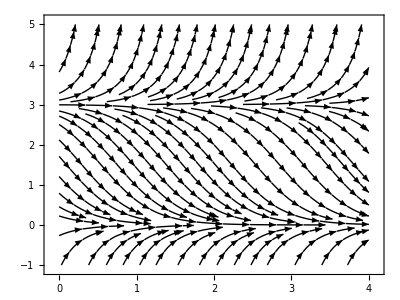

```mathematica
streamE=StreamPlot[{1,y(y-3)},{x,0,4},{y,-1,5},StreamStyle->Black,AspectRatio->3/4]
```

(f)

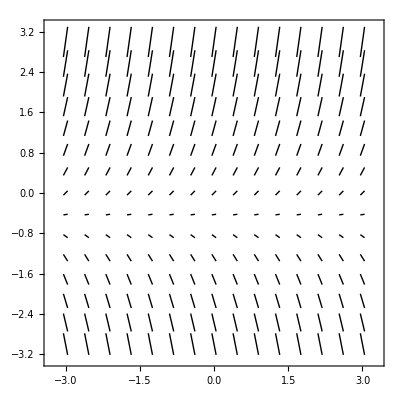

```mathematica
streamF=VectorPlot[{1,2y+1},{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black,Thick}]
```

(g) FIG 1.1.7

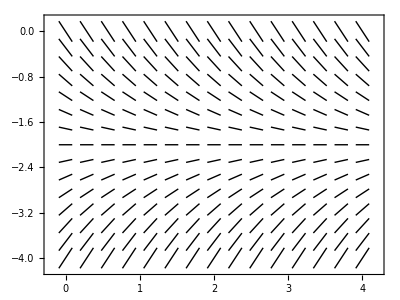

```mathematica
streamG=VectorPlot[{1,-2-y},{x,0,4},{y,-4,0},VectorStyle->{Arrowheads[0],Black,Thick},AspectRatio->3/4]
```

(h) FIG 1.1.9

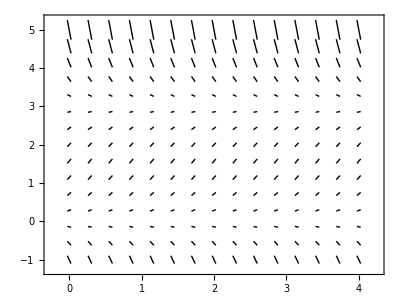

```mathematica
vectorH=VectorPlot[{1,y(3-y)},{x,0,4},{y,-1,5},VectorStyle->{Arrowheads[0],Black,Thick},AspectRatio->3/4]
```

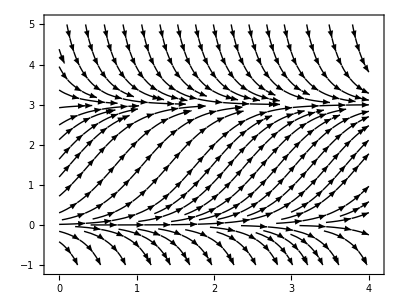

```mathematica
streamH=StreamPlot[{1,y(3-y)},{x,0,4},{y,-1,5},AspectRatio->3/4,StreamStyle->{Black}]
```

(i)

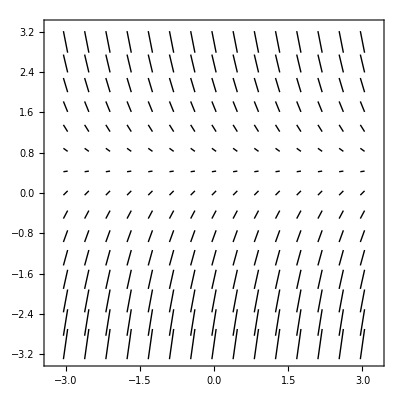

```mathematica
streamI=VectorPlot[{1,1-2y},{x,-3,3},{y,-3,3},VectorStyle->{Arrowheads[0],Black,Thick}]
```

(j) FIG 1.1.5

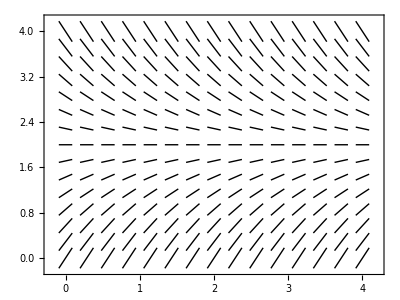

```mathematica
streamJ=VectorPlot[{1,2-y},{x,0,4},{y,0,4},VectorStyle->{Arrowheads[0],Black,Thick},AspectRatio->3/4]
```